```mathematica
(*Cèsar Muro Cabral*)
```

## Execute this line.

```mathematica
Needs["FourierSeries`"];
```

# Study of electromagnetically induced transparency and light propation on ensembles of Rubidium 87 cold atoms in the D2 line .

## Three level system.

We start with the three level model . We construct and solve the Bloch equations from the density matrix approach to obtain the susceptibility.  Then we plot the absorption and dispersion

```mathematica
MatrixForm[sys3={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}}];
MatrixForm[h7={{0,0,ΩP/2},{0,Δp-Δc,ΩC/2},{ΩP/2,ΩC/2,Δp}}];
TableForm[dt1=-{{0,0,0},{0,γ21,0},{0,0,Γ/2}}];
TableForm[leqs3=(I*(h7.sys3-sys3.h7))+dt1.sys3];
solg3=Simplify[Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, 21],leqs3[[3,1]]==-I*ω*Subscript[ρ, 31],χ3==Simplify[(Subscript[ρ, 31]/ΩP)]},{Subscript[ρ, 21],Subscript[ρ, 31],χ3}]/.{Subscript[ρ, 23]->0,Subscript[ρ, 33]->0,Subscript[ρ, 11]->1}];
χ3d=χ3/.solg3[[1]]
```

(2 (ⅈ γ21-Δc+Δp+ω))/(4 Δc Δp-4 Δp^2+2 Γ (γ21+ⅈ (Δc-Δp-ω))+4 Δc ω-8 Δp ω-4 ω^2-4 ⅈ γ21 (Δp+ω)+ΩC^2)

where Ωc is the control field, Δc,Δp are the detunings of the control and probe field, γ21=0.5Γ is the optical decoherence, and γ21=0.001Γ is the dephasing rate between the ground states. Therefore, from the previous result, we define the susceptibility

```mathematica
χΛ[ΩC_]:=(2 (ⅈ γ21-Δc+Δp+ω))/(4 Δc Δp-4 Δp^2+2 Γ (γ21+ⅈ (Δc-Δp-ω))+4 Δc ω-8 Δp ω-4 ω^2-4 ⅈ γ21 (Δp+ω)+ΩC^2)
```

And plot the absorption by employing the imaginary part of the susceptibility. Notice that as we increase the control field, we get a wider window of transparency, and when ΩC=0, then there is absorption

```mathematica
Manipulate[Plot[Im[χΛ[ΩC]/.{Γ->6.065,Δc->0,ω->0,γ21->0.001*6.065}],{Δp,-50,50},Frame->True,PlotRange->All,FrameLabel->{"δp(MHz)","Absorption Im χ"},Axes->False], {{ΩC,0,"Control field frequency"},0,40,5,Appearance->"Labeled"},SynchronousInitialization->False, SynchronousUpdating->False]
```

Now we plot the dispersion to see the effect of “slow light”

```mathematica
Manipulate[Plot[Re[χΛ[ΩC]/.{Γ->6.065,Δc->0,ω->0,γ21->0.001*6.065}],{Δp,-50,50},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"δp(MHz)","Dispersion Re χ"}], {{ΩC,0,"Control field frequency"},0,40,5,Appearance->"Labeled"},SynchronousInitialization->False, SynchronousUpdating->False]
```

## Four - level system (off resonant interaction)

Now, we consider that the atoms are pumped to the Zeeman sublevel F=1,m = 1. The control field is attached  is attached to the transition F=2,m=1→F’=2,m=2, with σ+ polarization, whereas the probe field to F=1,m=1→F’=2,m=2, with also σ+ polarization. In this four-level model,  we consider an off resonance interaction of the control field with the level F’=3,m=2. The hyperfine splitting between F’=2 and F’=1 is 266.65 MHz. Regarding the light propagation, we employ an initial Gaussian pulse with a temporal width of Tp=0.500.  Moreover, we write the Rabi frequency Rabi control in terms of the optical depth OD, i.e. Rabi=√((OD*Γ)/(ζ*Tp)). We obtain and solve the Bloch equations, plot the absorption Im[χ], the dispersion Re[χ] and the transmission with an optical depth of OD=275:

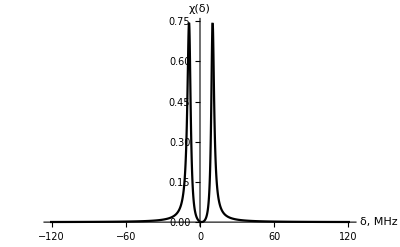

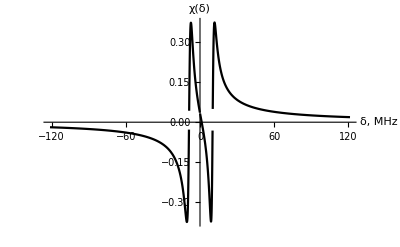

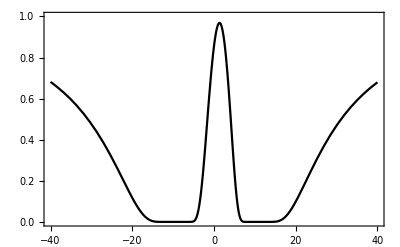

```mathematica
Γ=6.065;
j=3/2;
S=1/2;
IS=3/2;
hbar=1;
m=2;
γ21=0.0001*Γ;
hpf32=266.65;
γ31=0.5*Γ;
γ41=0.5*Γ;
OD=Table[OD=od ;OD,{od,0.00001,600,4}];
L001=Length[OD];
Tp=0.500;
ζ=2.0;
hbar=1;
Rabi=√((OD*Γ)/(ζ*Tp));
(*Probe field*)
Vp[Fe_,me_,Fg_,mg_]:=√(3/4*hbar*(2*j+1)*(2*Fg+1))*ClebschGordan[{Fg,mg},{1,me-mg},{Fe,me}]*SixJSymbol[{S,IS,Fg},{Fe,1,j}]*√Γ;
(*Control field, the dipole moment is obtained from the transtion strength, which is normalized respect to F=1,m=1->F'=2,m=2*)

Vc[Fe_,me_,Fs_,ms_]:=((ClebschGordan[{Fs,ms},{1,me-ms},{Fe,me}]*SixJSymbol[{S,IS,Fs},{Fe,1,j}])/(ClebschGordan[{2,1},{1,1},{2,2}]*SixJSymbol[{S,IS,Fs},{2,1,j}]))*Rabi/2;
MatrixForm[sys3={{Subscript[ρ, g3g3],Subscript[ρ, g3s3],Subscript[ρ, g3e4],Subscript[ρ, g3e5]},{Subscript[ρ, s3g3],Subscript[ρ, s3s3],Subscript[ρ, s3e4],Subscript[ρ, s3e5]},{Subscript[ρ, e4g3],Subscript[ρ, e4s3],Subscript[ρ, e4e4],Subscript[ρ, e4e5]},{Subscript[ρ, e5g3],Subscript[ρ, e5s3],Subscript[ρ, e5e4],Subscript[ρ, e5e5]}}];
MatrixForm[h7={{0,0,Subscript[ΩP, g3e4],0},{0,-Δc+Δp,Subscript[ΩC, s3e4],Subscript[ΩC, s3e5]},{Subscript[ΩP, g3e4],Subscript[ΩC, s3e4],+Δp,0},{0,Subscript[ΩC, s3e5],0,hpf32-Δc+Δp}}];
TableForm[dt1={{0,0,0,0},{0,γ21,0,0},{0,0,γ31,0},{0,0,0,γ41}}];
TableForm[leqs3=(I*(h7.sys3-sys3.h7))+dt1.sys3];
solg3=Solve[{leqs3[[2,1]]==-I*ω*Subscript[ρ, s3g3],leqs3[[3,1]]==-I*ω*Subscript[ρ, e4g3],leqs3[[4,1]]==-I*ω*Subscript[ρ, e5g3],Subscript[χ, g4l]==-Simplify[(Subscript[ρ, e4g3]*Subscript[ΩP, g3e4])]},{Subscript[ρ, s3g3],Subscript[ρ, e4g3],Subscript[ρ, e5g3],Subscript[χ, g4l]}]/.{Subscript[ρ, s3e4]->0,Subscript[ρ, e4e4]->0,Subscript[ρ, e5s3]->0,Subscript[ρ, e5e4]->0,Subscript[ρ, g3g3]->1};
Subscript[χ, pol4l]=Chop@Subscript[χ, g4l]/.solg3/.{Subscript[ΩC, s3e4]->Vc[2,2,2,1],Subscript[ΩC, s3e5]->Vc[3,2,2,1],Subscript[ΩP, g3e4]->Vp[2,2,1,1]};

Plot[{Evaluate[Im[Subscript[χ, pol4l][[1]][[16]]]/.{Δc->0,ω->0}]},{Δp,-20*Γ,20*Γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]
Plot[{Evaluate[Re[Subscript[χ, pol4l][[1]][[16]]]/.{Δc->0,ω->0}]},{Δp,-20*Γ,20*Γ},AxesOrigin->{0,0},PlotRange->All,PlotStyle->Black,AxesLabel->TraditionalForm/@{"δ, MHz"," χ(δ)"}]

Plot[Exp[-((Γ/2)*OD[[16]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[16]]/.{Δc->0,ω->0})]]],{Δp,-40,40},PlotStyle->Black,PlotRange->{0,1.0},Frame->True]
```

Now we construct a table called “det”, with the detunings  Δp’s where the transmission achieves the maximum for each optical depth.

```mathematica
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]])*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ΔD->0,ω->0})]]],-50<=Δp<=0},{Δp,-1}]],{i,1,L001}]
```

{-10.4141,-0.316885,-0.6323,-0.946267,-1.25881,-1.56994,-1.87968,-2.18805,-2.49506,-2.80075,-3.10511,-3.40818,-3.70996,-4.01048,-4.30975,-4.60778,-4.90459,-5.2002,-5.49463,-5.78787,-6.07996,-6.3709,-6.66071,-6.9494,-7.23699,-7.52348,-7.80889,-8.09324,-8.37652,-8.65877,-8.93999,-9.22018,-9.49937,-9.77756,-10.0548,-10.331,-10.6062,-10.8806,-11.1539,-11.4263,-11.6978,-11.9684,-12.2381,-12.5069,-12.7748,-13.0418,-13.308,-13.5733,-13.8377,-14.1013,-14.3641,-14.626,-14.8871,-15.1474,-15.4069,-15.6657,-15.9236,-16.1807,-16.4371,-16.6927,-16.9475,-17.2016,-17.455,-17.7076,-17.9595,-18.2107,-18.4611,-18.7108,-18.9599,-19.2082,-19.4558,-19.7028,-19.949,-20.1946,-20.4396,-20.6838,-20.9274,-21.1704,-21.4127,-21.6543,-21.8954,-22.1358,-22.3755,-22.6147,-22.8532,-23.0912,-23.3285,-23.5652,-23.8013,-24.0369,-24.2718,-24.5062,-24.74,-24.9732,-25.2059,-25.438,-25.6695,-25.9005,-26.1309,-26.3608,-26.5901,-26.8189,-27.0472,-27.2749,-27.5021,-27.7288,-27.955,-28.1806,-28.4058,-28.6304,-28.8545,-29.0782,-29.3013,-29.5239,-29.7461,-29.9678,-30.1889,-30.4096,-30.6299,-30.8496,-31.0689,-31.2877,-31.5061,-31.724,-31.9414,-32.1584,-32.3749,-32.591,-32.8066,-33.0218,-33.2366,-33.4509,-33.6648,-33.8782,-34.0913,-34.3039,-34.5161,-34.7278,-34.9392,-35.1501,-35.3606,-35.5707,-35.7804,-35.9897,-36.1986,-36.4071,-36.6152,-36.8229,-37.0302,-37.2371,-37.4437,-37.6498,-37.8556,-38.061,-38.266,-38.4706,-38.6749,-38.8788,-39.0823,-39.2855,-39.4883,-39.6907,-39.8928,-40.0945,-40.2958,-40.4968,-40.6975,-40.8977,-41.0977,-41.2973,-41.4965,-41.6955,-41.894,-42.0923,-42.2902,-42.4877,-42.6849,-42.8818,-43.0784,-43.2746,-43.4705,-43.6661,-43.8614,-44.0563,-44.2509,-44.4452,-44.6392,-44.8329,-45.0263,-45.2193,-45.4121,-45.6045,-45.7966,-45.9884,-46.18,-46.3712,-46.5621,-46.7527,-46.943,-47.1331}

We write the inital Gaussian pulse as Wp0[ω]= Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])]. To compute the optical storage-efficiency, we analyze two equivalent approaches: -integrating in ω-frequency domain and 
- numerical Fourier transform. 
We construct the output pulse at the end of the ensmeble  as ϵ_out=Wp0[ω]*Exp[-((Γ/2)*OD[[i]]/(Vp[4,4,3,3]^2))*Evaluate[Im[(χ_pol4l[[1]][[i]]/.{Δc→0,Δp->det[[i]]})]]], and the efficiency of the optical memory is estimated as (∫_(-∞)^∞ |ϵ_out|^2 ⅆω)/(∫_(-∞)^∞ |ϵ_in|^2 ⅆω) , and  (∫_(-∞)^∞ |ϵ_out|^2 ⅆt)/(∫_(-∞)^∞ |ϵ_in|^2 ⅆt).Therefore

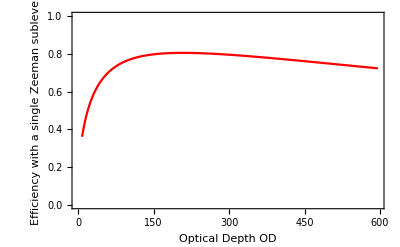

```mathematica
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ω->0})]]],0<=Δp<=35},{Δp,1}]],{i,1,L001}];
Wp0[ω_]:=Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
(*I store the out pulse in a table being every element the corresponding for for every optical depth*)
ϵ3d2out=Table[Wp0[ω]*Exp[-((Γ/4)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,Δp->det[[i]]})]]],{i,1,L001}];
(*Then I follow the formula (14) for the the slow light transmission efficiency  "Broadband coherent optical memory"*)
eff4l=Table[NIntegrate[Abs[ϵ3d2out[[i]]]^2,{ω,-∞,∞}]/NIntegrate[Abs[Wp0[ω]]^2,{ω,-∞,∞}],{i,1,L001}];
data4l=Transpose@{OD,eff4l};
(*As you can see large optical depth*)
ListPlot[Delete[data4l,{{1},{2}}],Frame->True,PlotRange->{All,{0,1.0}},Joined->True,PlotStyle->{Black,Red},FrameLabel->{"Optical Depth OD","Efficiency with a single Zeeman sublevel"}]
```

Numerical Fourier Transform function throught Mathematica function NInverseFourier transform. We have to run the first line of the code. The time interval where we calculate the Fourier transform (thus the efficiency) is from -6 to 6, in steps size of 0.25.

```mathematica
τ=Table[τ=tim;τ,{tim,-6,6,0.25}];
OD=Table[OD=od ;OD,{od,0.00001,600,4}];
Wp0[ω_]:=Tp/(√(4Log[2]))*Exp[(-ω^2 Tp^2)/(8*Log[2])];
L001=Length[OD];
det=Table[Δp/.Last[FindMaximum[{Exp[-((Γ/2)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,ω->0})]]],0<=Δp<=35},{Δp,1}]],{i,1,L001}];

ϵ3d2out=Table[Wp0[ω]*Exp[-((Γ/4)*OD[[i]]/(Vp[2,2,1,1]^2))*Evaluate[Im[(Subscript[χ, pol4l][[1]][[i]]/.{Δc->0,Δp->det[[i]]})]]],{i,1,L001}];
ft4l=Table[Chop@NInverseFourierTransform[ϵ3d2out[[h]],ω,i],{h,2,L001},{i,-6,6,.25}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {2.74411}. NIntegrate obtained 4.34702×10^-10-8.59438×10^-11 ⅈ and 5.80554×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.71493×10^-10+1.98263×10^-10 ⅈ and 3.88714×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.71493×10^-10-1.98263×10^-10 ⅈ and 3.88714×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.00131×10^-10+4.03265×10^-12 ⅈ and 3.89273×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
ϵsZ=Transpose@{Delete[OD,{{1}}],Chop@Table[NIntegrate[(Interpolation[Transpose@{τ,ft4l[[i]]},InterpolationOrder->3][t])^2,{t,-8,8}]/NIntegrate[Wp0[ω]^2,{ω,-∞,∞}],{i,1,Length[ft4l]}]}
ListPlot[{Delete[data4l,{{1},{2}}],Insert[ϵsZ,{0,0},1]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,18]]
```

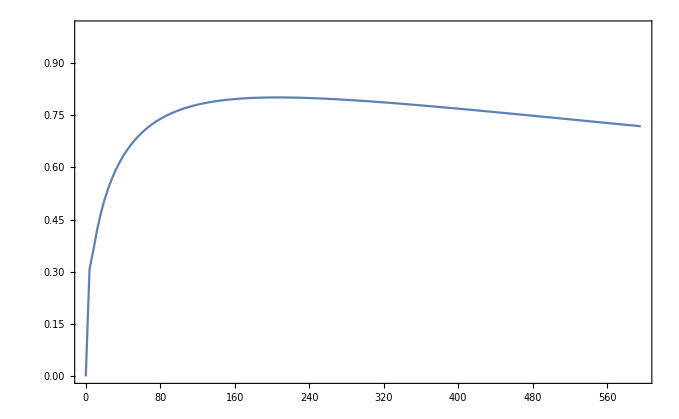

```mathematica
ListPlot[{Insert[ϵsZ,{0,0},1]},Joined->True,PlotRange->{0,1.0},Frame->True,FrameTicksStyle->Directive[Black,18],PlotRangePadding->None]
```

We observe that the efficiency achieves a maximum of 80% around an optical depth of 140, after that,  it tends to decrease slowly.